```mathematica
Remove["Global`*"]
```

## Library ComplexMatrixDraw (copy to your Notebook, evaluate and use the complexMatrixDraw function)

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=Append[position+{-0.5,1.5},0]+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{center+{-0.5,-0.5,0},center+{0.5,-0.5,0},center+{0.5,0.5,0},center+{-0.5,0.5,0}}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[center-OptionValue[barDiameter]{0.5,0.5,0},center+OptionValue[barDiameter]{0.5,0.5,0}+{0,0,val}],
_,Cylinder[{center,center+{0,0,val}},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{center+{0,0,val},center+{0,0,val}+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

## Data Import

```mathematica
replacements={"j"->"ⅈ","e"->"*10^"};
myImport[fileName_,type_,headerLines_:0,printHeader_:False]:=
Block[
{data=Import[fileName,type],depth},
depth=data//dimensions//Length;
If[printHeader,Print["Header: "<>ToString[Take[data,headerLines]]]];
data=(Map[StringReplace[#,replacements]&,Drop[data,headerLines],{depth}])// ToExpression
]
```

```mathematica
data=myImport[NotebookDirectory[]<>"film 300 - fitted density matrices.txt","Table",1,False];
```

```mathematica
tomos=Map[Partition[#,4]&,data];
```

```mathematica
Remove["barColorFunc"]
barColorFunc=
Block[{hsbcolor=
ColorConvert[RGBColor[
Cos[#2/2]^2,
Sin[#2]/2+0.5,
1.0-Cos[#2/2]^2
]
,"HSB"]
}
,Hue[hsbcolor[[1]],hsbcolor[[2]]*0.5,hsbcolor[[3]]*1.5]]&;
```

```mathematica
probs = Transpose[Map[{Abs[#[[1,1]]],Abs[#[[2,2]]],Abs[#[[3,3]]],Abs[#[[4,4]]]}&,tomos]];
```

```mathematica
probsWithX=Map[Block[{list=#},MapIndexed[{(#2[[1]]-1)*2,#1}&,list]]&,probs];
```

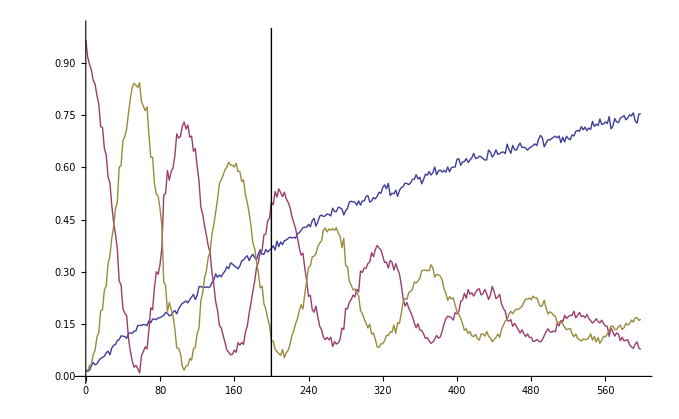

```mathematica
ListPlot[{probsWithX[[1]],probsWithX[[2]],probsWithX[[3]]},Joined->True,PlotRange->{0,1},Epilog->Line[{{200,0},{200,1}}],PlotStyle->{FontFamily->"Arial"}]
```

```mathematica
tomoMatrices=Map[matrixDraw3D[#,whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Black,Thickness[0.01],Arrowheads[0]},barDiameter->0.4,arrowLength->(0.3&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&),barColorFunction->barColorFunc]&,tomos];
```

```mathematica
plots = Show[#,ViewPoint->10000{0.2,-1.1,1.5},BoxRatios->{1,1,0.5},Boxed->False,PlotRange->{All,All,{0,1}}]&/@tomoMatrices;
```

```mathematica
toFixedWidth[n_Integer,width_Integer]:=StringJoin[PadLeft[Characters[ToString[n]],width,"0"]]
```

```mathematica
Remove["probPlot"]
probPlot[t_] := ListPlot[{probsWithX[[1]],probsWithX[[2]],probsWithX[[3]]},Joined->True,PlotRange->{0,1},Epilog->Line[{{t,0},{t,1}}],PlotStyle->{Darker[Green],Blue,Red},BaseStyle->{FontFamily->"Arial",FontSize->6}];
```

```mathematica
catAlive = Import[NotebookDirectory[]<>"cat_alive.png"];
catDead = Import[NotebookDirectory[]<>"cat_dead.png"];
```

```mathematica
MapIndexed[Export[NotebookDirectory[]<>"matrices/matrix_"<>toFixedWidth[#2[[1]],3]<>".gif",GraphicsGrid[{{#1,probPlot[#2[[1]]*2]},{
ImagePad[SetAlphaChannel[ImageCompose[catDead,{catAlive,probs[[2]][[#2[[1]]]]/(probs[[2]][[#2[[1]]]]+probs[[3]][[#2[[1]]]])}]],50+600*(probs[[1]][[#2[[1]]]]),White]}}],ImageResolution->300]&,plots];
```

DeleteFile::privv: Privilege violation during DeleteFile["C:\\Users\\Heisenberg\\AppData\\Local\\Temp\\m-d66c653e-d935-4fba-9637-beac149c4a25.rdp"].

DeleteFile::privv: Privilege violation during DeleteFile["C:\\Users\\Heisenberg\\AppData\\Local\\Temp\\m-e2c5bd2c-8c7a-44f8-88eb-7a13887e34ee.rdp"].

DeleteFile::privv: Privilege violation during DeleteFile["C:\\Users\\Heisenberg\\AppData\\Local\\Temp\\m-4a410162-f31f-4eb1-8314-f4e8792af51c.rdp"].

General::stop: Further output of DeleteFile :: privv will be suppressed during this calculation.

$Aborted

```mathematica
Export[NotebookDirectory[]<>"matrices/test.png",,ImageResolution->150]
```

D:\cygwin\home\adewes\thesis\data\ct5\film of swap\matrices/test.png

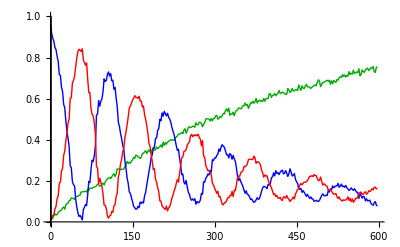

```mathematica
probPlot[1]
```

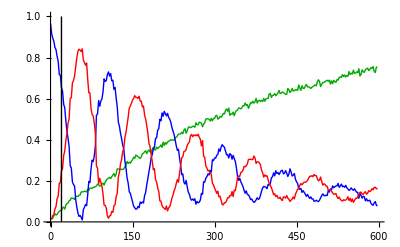

```mathematica
GraphicsGrid[{{plots[[1]],probPlot[10*2]},{ImagePad[
SetAlphaChannel[
ImageCompose[
catAlive,
{catDead,probs[[2]][[10]]/(probs[[2]][[10]]+probs[[3]][[10]])}]],
5000,White]}}]
```

```mathematica
ImagePad[SetAlphaChannel[ImageCompose[catAlive,{catDead,probs[[2]][[10]]/(probs[[2]][[10]]+probs[[3]][[10]])}]],2000*probs[[1]][[10]]]
```

-Graphics-